## Plotting functions given output of GeomComp_Compute.nb

## Preliminaries

```mathematica
Clear["Global`*"]
SetDirectory[FileNameJoin[{NotebookDirectory[],"results/"}]] ;
files=FileNames["*.txt"] (* Get list of all result files *)
Get[#]&/@files; (* Load all their contents (variable definitions) *)
SetDirectory[FileNameJoin[{NotebookDirectory[],"../figs/"}]] ;
```

{P1fixH1.txt,P1fixR.txt,P1varH1.txt,P1varR.txt,P2fixA1.txt,P2fixA3.txt,P2fixAG.txt,P2fixGIA.txt,P2fixGI.txt,P2fixH2.txt,P2fixH3.txt,P2fixHT.txt,P2fixHV.txt,P2fixSH.txt,P2varA1.txt,P2varA3.txt,P2varAG.txt,P2varGIA.txt,P2varGI.txt,P2varH2.txt,P2varH3.txt,P2varHT.txt,P2varHV.txt,P2varSH.txt,P3fixA2.txt,P3fixAA.txt,P3fixBD.txt,P3fixBWL.txt,P3fixCM.txt,P3fixHLB.txt,P3fixMH.txt,P3fixTTA.txt,P3varA2.txt,P3varAA.txt,P3varBD.txt,P3varBWL.txt,P3varCM.txt,P3varHLB.txt,P3varMH.txt,P3varTTA.txt}

### Function to append relative (ratios of) complexity values

Denom_ is the measure to which the Numer_ measures are compared

```mathematica
Relativize[dataDenom_,dataNumer_]:=Join[dataNumer[[All,{1,2}]],Transpose[{dataNumer[[All,3]]/dataDenom[[All,3]]}],2];
```

### Define generic plotting function

```mathematica
MyListLinePlot[
data_,
axislabels_,
plotlabel_,
plotRange_]:=
ListLinePlot[Apply[{#1,#3}&,
SortBy[Cases[Normal@
ListPlot3D[
data,
PlotRange->All,
InterpolationOrder->1,
Mesh-> {{0},DeleteDuplicates[data[[All,2]]]},
ScalingFunctions->{"Linear","Linear","Linear"},
BoundaryStyle->None,
Boxed->False,
Axes->False],
Line[a_]:>a,Infinity],{2}],
{2}],
ScalingFunctions->{"Log","Log"}, 
PlotStyle->ColorData[49,"ColorList"],
GridLines->{None,{1}},
GridLinesStyle->Directive[LightGray, Dashed],
PlotRange->plotRange,
Frame-> True,
FrameLabel-> axislabels,
PlotLabel->plotlabel]
```

## Plot ratio of Geometric complexities - varying max abundance levels

```mathematica
axislabelsLineComp={"Max. prey abundance","Flexibility"};
axislabelsLineRel={"Max. prey abundance","Relative flexibility"};
axislabelsLineComp2={"Max. prey abundance",""};
axislabelsLineRel2={"Max. prey abundance",""};
```

```mathematica
p1varH1=MyListLinePlot[
varH1,
axislabelsLineComp,
"Holling Type I",
{All,All}
];
p1varH1vR=MyListLinePlot[
Relativize[varH1,varR],
axislabelsLineRel,
"Ratio / Holling Type I",
{All,{All,1}}
];
```

```mathematica
p2varH2=MyListLinePlot[
varH2,
axislabelsLineComp2,
"Holling Type II",
{All,{3,8.5}}
];
p2varH2vHV=MyListLinePlot[
Relativize[varH2,varHV],
axislabelsLineRel2,
"Hassell-Varley / Holling Type II",
{All,{0.98,All}}
];
p2varH2vAG=MyListLinePlot[
Relativize[varH2,varAG],
axislabelsLineRel,
"Arditi-Ginzburg / Holling Type II",
{All,{0.98,All}}
];
```

```mathematica
p3varBD=MyListLinePlot[
varBD,
axislabelsLineComp2,
"Beddington-DeAngelis",
{All,All}
];
p3varBDvCM=MyListLinePlot[
Relativize[varBD,varCM],
axislabelsLineRel2,
"Crowley-Martin / Beddington-DeAngelis",
{All,{0.98,All}}
];
p3varBDvAA=MyListLinePlot[
Relativize[varBD,varAA],
axislabelsLineRel2,
"Arditi-Akcakaya / Beddington-DeAngelis",
{All,{0.98,All}}
];
```

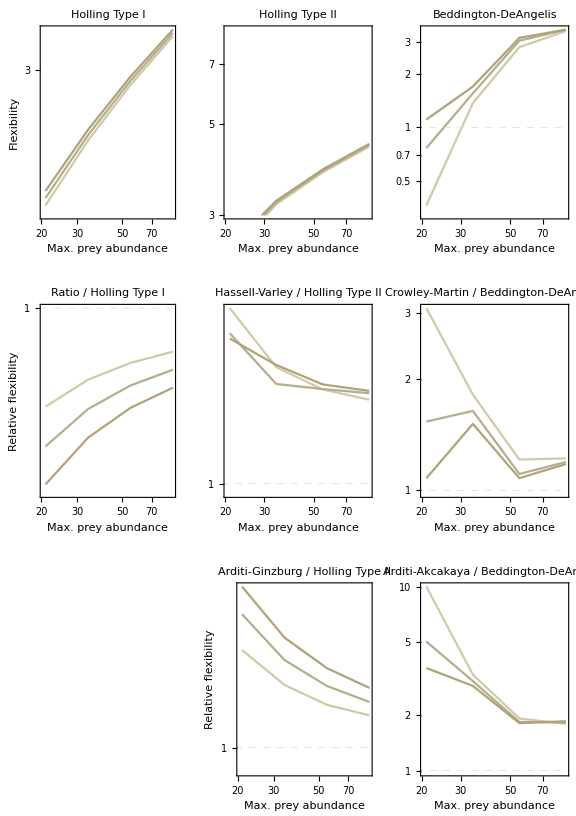

```mathematica
AllVar=
Legended[
GraphicsGrid[{
{p1varH1,p2varH2,p3varBD},
{p1varH1vR,p2varH2vHV,p3varBDvCM},
{"",p2varH2vAG,p3varBDvAA}},
ImageSize-> Large],
Placed[
LineLegend[
ColorData[49,"ColorList"],
DeleteDuplicates[varH1[[All,2]]],
LegendLabel->"Max. predator abundance",
LegendLayout->"Row"],
Above]]

Export["GeomComp_var.pdf",AllVar];
```

## Plot ratio of Geometric complexities - fixed max abundance levels

```mathematica
axislabelsLineComp={"Prey levels","Flexibility"};
axislabelsLineRel={"Prey levels","Relative flexibility"};
axislabelsLineComp2={"Prey levels",""};
axislabelsLineRel2={"Prey levels",""};
```

```mathematica
p1fixH1=MyListLinePlot[
fixH1,
axislabelsLineComp,
"Holling Type I",
{All,All}
];
p1fixH1vR=MyListLinePlot[
Relativize[fixH1,fixR],
axislabelsLineRel,
"Ratio / Holling Type I",
{All,{All,1.001}}
];
```

```mathematica
p2fixH2=MyListLinePlot[
fixH2,
axislabelsLineComp2,
"Holling Type II",
{All,All}
];
p2fixH2vHV=MyListLinePlot[
Relativize[fixH2,fixHV],
axislabelsLineRel2,
"Hassell-Varley / Holling Type II",
{All,{0.99,All}}
];
p2fixH2vAG=MyListLinePlot[
Relativize[fixH2,fixAG],
axislabelsLineRel,
"Arditi-Ginzburg / Holling Type II",
{All,{0.99,All}}
];
```

```mathematica
p3fixBD=MyListLinePlot[
fixBD,
axislabelsLineComp2,
"Beddington-DeAngelis",
{All,All}
];
p3fixBDvCM=MyListLinePlot[
Relativize[fixBD,fixCM],
axislabelsLineRel2,
"Crowley-Martin / Beddington-DeAngelis",
{All,{0.98,All}}
];
p3fixBDvAA=MyListLinePlot[
Relativize[fixBD,fixAA],
axislabelsLineRel2,
"Arditi-Akcakaya / Beddington-DeAngelis",
{All,{0.98,All}}
];
```

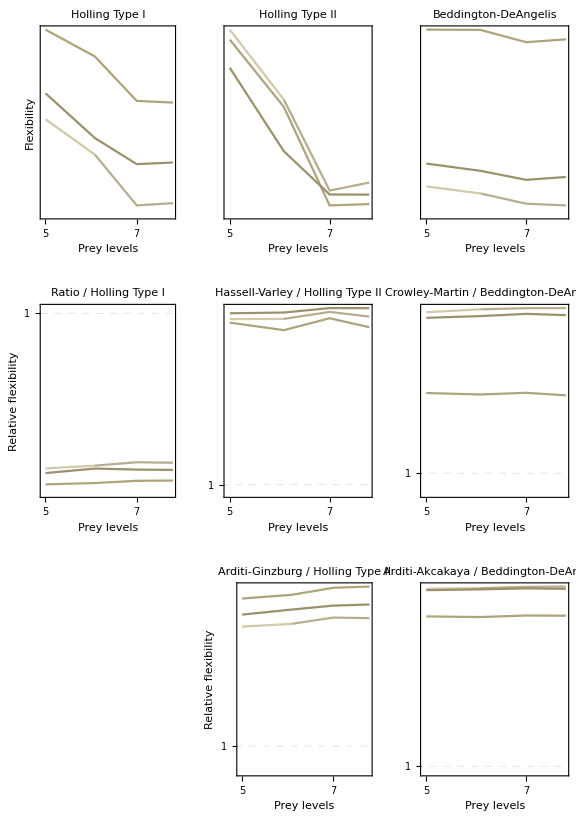

```mathematica
AllFix=
Legended[
GraphicsGrid[{
{p1fixH1,p2fixH2,p3fixBD},
{p1fixH1vR,p2fixH2vHV,p3fixBDvCM},
{"",p2fixH2vAG,p3fixBDvAA}},
ImageSize-> Large],
Placed[
LineLegend[
ColorData[49,"ColorList"],
DeleteDuplicates[fixH1[[All,2]]],
LegendLabel->"Predator levels",
LegendLayout->"Row"],
Above]]

Export["GeomComp_fix.pdf",AllFix];
```